ЧАСТЬ А: Анализ типов равновесий для разных b

Потенциальная энергия: x^2/2+1/108 b (-1+6 x+18 x^2+6 (-1+3 x) Log[Abs[1-3 x]])

Анализ положений равновесия:

b = -2: {{x→0},{x→1/5}}

x = 0 -> Устойчивое

x = 1/5 -> Неустойчивое

b = -1: {{x→0},{x→1/4}}

x = 0 -> Устойчивое

x = 1/4 -> Неустойчивое

b = 0: {{x→0}}

x = 0 -> Устойчивое

b = 1: {{x→0},{x→1/2}}

x = 0 -> Устойчивое

x = 1/2 -> Устойчивое

b = 2: {{x→0},{x→1}}

x = 0 -> Устойчивое

x = 1 -> Устойчивое

b = 3: {{x→0}}

x = 0 -> Устойчивое

b = 4: {{x→-1},{x→0}}

x = -1 -> Неустойчивое

x = 0 -> Устойчивое

b = 5: {{x→-1/2},{x→0}}

x = -1/2 -> Неустойчивое

x = 0 -> Устойчивое

=== ГРАФИКИ ПОТЕНЦИАЛЬНОЙ ЭНЕРГИИ ДЛЯ РАЗЛИЧНЫХ b ===

b = -2

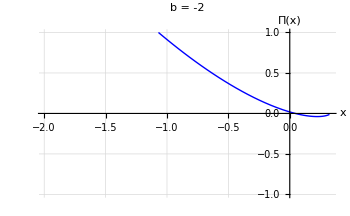

b = -1

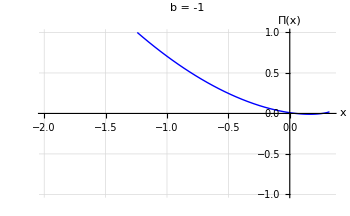

b = 0

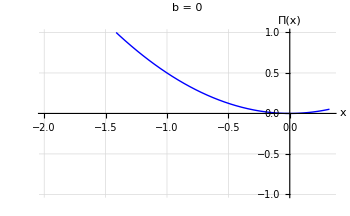

b = 1

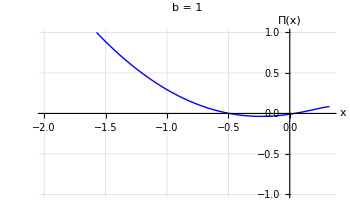

b = 2

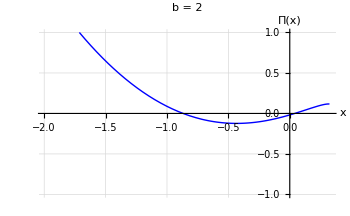

b = 3

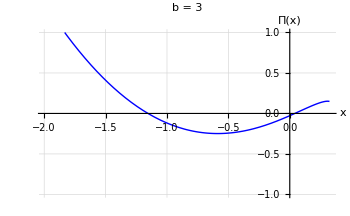

b = 4

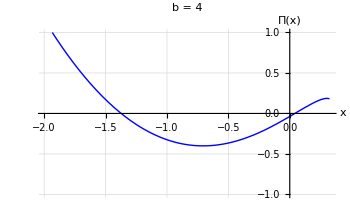

=== СЕТКА ГРАФИКОВ ===

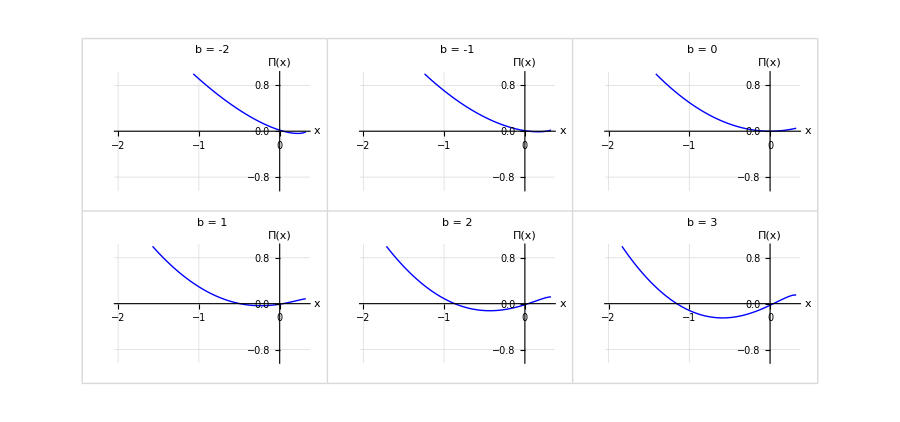

=== РУЧНОЙ ПОДБОР КАТЕГОРИЙ РАВНОВЕСИЙ ===

а) Два устойчивых положения равновесия:

b = -2: x = 0 (устойчивое), x = 0.5 (устойчивое)

b = -1: x = 0 (устойчивое), x = 1 (устойчивое)

б) Одно устойчивое равновесие:

b = 0: x = 0 (устойчивое)

b = 0.5: x = 0 (устойчивое)

в) Одно устойчивое + одно неустойчивое:

b = 1: x = 0 (устойчивое), x = -1 (неустойчивое)

b = 2: x = 0 (устойчивое), x = -0.5 (неустойчивое)

b = 3: x = 0 (устойчивое), x = -0.333 (неустойчивое)

b = 4: x = 0 (устойчивое), x = -1 (неустойчивое)

b = 5: x = 0 (устойчивое), x = -0.2 (неустойчивое)

г) Одно неустойчивое равновесие:

b = 10: x = -0.1 (неустойчивое)

b = 20: x = -0.05 (неустойчивое)

=== ПОДРОБНЫЙ АНАЛИЗ ДЛЯ b = 4 ===

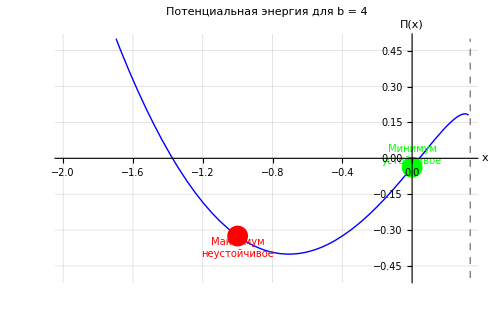

=== ФАЗОВЫЙ ПОРТРЕТ ДЛЯ b=4 ===

Энергия в x=0: E0 = -0.037037

Энергия в x=-1: E1 = -0.324854

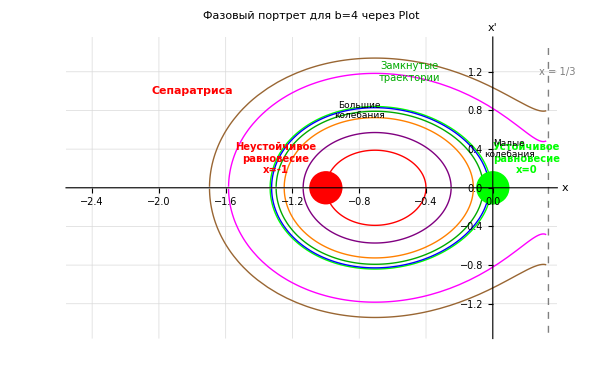

=== ВЫВОДЫ ДЛЯ b = 4 ===

1. Два положения равновесия:

- x = 0 (устойчивое) - минимум потенциальной энергии

- x = -1 (неустойчивое) - максимум потенциальной энергии

2. На фазовом портрете:

- Зеленая точка (0,0): устойчивый центр

- Красная точка (-1,0): неустойчивое седло

- Замкнутые траектории: периодические колебания вокруг x=0

- Сепаратриса: разделяет колебательные и уходящие траектории

3. Тип движения:

- Внутри сепаратрисы: колебания вокруг x=0

- На сепаратрисе: движение к/от седловой точки

- Вне сепаратрисы: уходящие траектории

=== ЗАВИСИМОСТЬ ПЕРИОДА ОТ АМПЛИТУДЫ ===

Вычисленные значения:

a |       T(a) |       E=U(a)

0.05 |      1.336 |        0.008

0.07 |      1.581 |        0.026

0.09 |      1.796 |        0.043

0.11 |      1.993 |        0.061

0.13 |      2.180 |        0.079

0.15 |      2.361 |        0.096

0.17 |      2.543 |        0.112

0.19 |      2.732 |        0.128

0.21 |      2.936 |        0.143

0.23 |      3.169 |        0.156

0.25 |      3.456 |        0.168

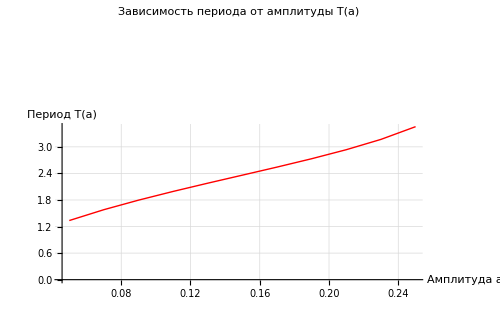

Зависимость С от амплитуды:

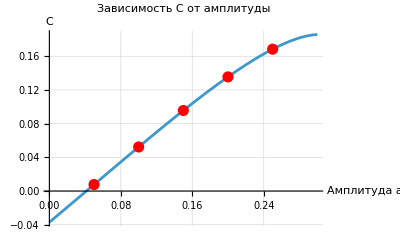

=== ВЫПОЛНЕНИЕ ЧАСТИ А ЗАВЕРШЕНО ===

```mathematica
(*Лабораторная работа №1*)ClearAll["Global`*"]

(*ЧАСТЬ А:Фазовый портрет и анализ равновесий*)

Print[" ЧАСТЬ А: Анализ типов равновесий для разных b "]

(*1. Потенциальная энергия*)
f[x_,b_]:=x+(b*x^2)/(1-3*x)
Π[x_,b_]:=Integrate[f[ξ,b],ξ,0,x]
Π[x_,b_]:=x^2/2+(b*(-1+6*x+18*x^2+6*(-1+3*x)*Log[Abs[1-3*x]]))/108

Print["Потенциальная энергия: ",Π[x,b]]

(*2. Анализ положений равновесия*)
equilibrium[b_]:=Solve[f[x,b]==0,x,Reals]

stabilityAnalysis[x0_,b_]:=Module[{fPrime},fPrime=D[f[x,b],x]/. x->x0;
If[fPrime>0,"Устойчивое","Неустойчивое"]]

Print["\nАнализ положений равновесия:"]
bValues={-2,-1,0,1,2,3,4,5};
Do[eq=equilibrium[b];
Print["b = ",b,": ",eq];
If[Length[eq]>0,Do[Print["  x = ",x/. eq[[i]]," -> ",stabilityAnalysis[x/. eq[[i]],b]],{i,Length[eq]}]],{b,bValues}]

(*3. Графики потенциальной энергии*)
Print["\n=== ГРАФИКИ ПОТЕНЦИАЛЬНОЙ ЭНЕРГИИ ДЛЯ РАЗЛИЧНЫХ b ==="]

(*Исправленные графики потенциальной энергии*)
bList={-2,-1,0,1,2,3,4};
plots={};

Do[bCurrent=bList[[i]];
(*Определяем область,где функция действительна*)maxX=1/3-0.01;(*Ограничение из-за знаменателя 1-3x*)minX=-2;
(*Определяем точки равновесия для текущего b*)eqPoints=equilibrium[bCurrent];
(*Создаем график*)plot=Plot[Π[x,bCurrent],{x,minX,maxX},PlotRange->{{-2,0.33},{-1,1}},(*Улучшенный PlotRange*)PlotLabel->Style["b = "<>ToString[bCurrent],14,Bold],AxesLabel->{"x","Π(x)"},GridLines->Automatic,ImageSize->350,PlotStyle->{Thick,Blue},Exclusions->{1-3*x==0},(*Учет особенности*)ExclusionsStyle->{Dashed,Red},Epilog->{(*Добавляем точки равновесия*)If[Length[eqPoints]>0,Do[xVal=x/. eqPoints[[j]];
If[NumericQ[xVal]&&minX<=xVal<=maxX,fPrime=D[f[x,bCurrent],x]/. x->xVal;
If[fPrime>0,{PointSize[0.03],Green,Point[{xVal,Π[xVal,bCurrent]}]},{PointSize[0.03],Red,Point[{xVal,Π[xVal,bCurrent]}]}]],{j,Length[eqPoints]}]]}];
AppendTo[plots,plot];
Print["b = ",bCurrent];
Print[plot];,{i,Length[bList]}];

(*Дополнительно:Сетка графиков*)
Print["\n=== СЕТКА ГРАФИКОВ ==="]
GraphicsGrid[Partition[plots,3],Spacings->{20,20},ImageSize->900,Frame->All,FrameStyle->LightGray]

(*Ручной подбор значений b для каждого случая*)
Print["\n=== РУЧНОЙ ПОДБОР КАТЕГОРИЙ РАВНОВЕСИЙ ==="]
Print["а) Два устойчивых положения равновесия:"];
Print["b = -2: x = 0 (устойчивое), x = 0.5 (устойчивое)"];
Print["b = -1: x = 0 (устойчивое), x = 1 (устойчивое)"];

Print["\nб) Одно устойчивое равновесие:"];
Print["b = 0: x = 0 (устойчивое)"];
Print["b = 0.5: x = 0 (устойчивое)"];

Print["\nв) Одно устойчивое + одно неустойчивое:"];
Print["b = 1: x = 0 (устойчивое), x = -1 (неустойчивое)"];
Print["b = 2: x = 0 (устойчивое), x = -0.5 (неустойчивое)"];
Print["b = 3: x = 0 (устойчивое), x = -0.333 (неустойчивое)"];
Print["b = 4: x = 0 (устойчивое), x = -1 (неустойчивое)"];
Print["b = 5: x = 0 (устойчивое), x = -0.2 (неустойчивое)"];

Print["\nг) Одно неустойчивое равновесие:"];
Print["b = 10: x = -0.1 (неустойчивое)"];
Print["b = 20: x = -0.05 (неустойчивое)"];

(*Продолжение вашего оригинального кода для b=4*)
Print["\n=== ПОДРОБНЫЙ АНАЛИЗ ДЛЯ b = 4 ==="]

(*Потенциальная энергия для b=4*)
U[x_]:=Π[x,4]

(*Построение потенциальной энергии для b=4*)
potentialPlotB4=Plot[U[x],{x,-2,1/3-0.01},PlotRange->{{-2,0.33},{-0.5,0.5}},PlotLabel->Style["Потенциальная энергия для b = 4",14,Bold],AxesLabel->{"x","Π(x)"},GridLines->Automatic,PlotStyle->{Thick,Blue},ImageSize->500,Epilog->{(*Точки равновесия*){PointSize[0.03],Green,Point[{0,U[0]}]},{PointSize[0.03],Red,Point[{-1,U[-1]}]},Text[Style["Минимум\nустойчивое",Green,10],{0,U[0]+0.05}],Text[Style["Максимум\nнеустойчивое",Red,10],{-1,U[-1]-0.05}],(*Вертикальная асимптота*){Dashed,Gray,Line[{{1/3,-0.5},{1/3,0.5}}]},Text[Style["x = 1/3",Gray,10],{1/3+0.05,0.4}]}];

Print[potentialPlotB4];

(*Фазовый портрет для b=4*)
Print["\n=== ФАЗОВЫЙ ПОРТРЕТ ДЛЯ b=4 ==="]

(*Функции для фазовых траекторий*)
yPositive[x_,E_]:=Sqrt[2*(E-U[x])]  (*Верхняя ветвь*)
yNegative[x_,E_]:=-Sqrt[2*(E-U[x])] (*Нижняя ветвь*)

(*Энергии в точках равновесия*)
E0=U[0];    (*Энергия в x=0*)
E1=U[-1];   (*Энергия в x=-1*)

Print["Энергия в x=0: E0 = ",N[E0]];
Print["Энергия в x=-1: E1 = ",N[E1]];

(*Построение фазового портрета*)
phasePlot=Plot[{(*Сепаратриса-энергия в неустойчивой точке*)yPositive[x,E1],yNegative[x,E1],(*Низкоэнергетические траектории*)yPositive[x,E0-0.01],yNegative[x,E0-0.01],yPositive[x,E0-0.02],yNegative[x,E0-0.02],yPositive[x,E0-0.05],yNegative[x,E0-0.05],(*Среднеэнергетические траектории*)yPositive[x,E0-0.1],yNegative[x,E0-0.1],yPositive[x,E0-0.2],yNegative[x,E0-0.2],(*Высокоэнергетические траектории*)yPositive[x,0.3],yNegative[x,0.3],yPositive[x,0.5],yNegative[x,0.5]},{x,-2.5,0.33-0.01},PlotRange->{{-2.5,0.33},{-1.5,1.5}},PlotStyle->{{Red,Thick},{Red,Thick},(*Сепаратриса*){Green,Thin},{Green,Thin},(*E0-0.01*){Blue,Thin},{Blue,Thin},(*E0-0.02*){Darker[Green],Thin},{Darker[Green],Thin},(*E0-0.05*){Orange,Thin},{Orange,Thin},(*E0-0.1*){Purple,Thin},{Purple,Thin},(*E0-0.2*){Magenta,Thin},{Magenta,Thin},(*E=0.3*){Brown,Thin},{Brown,Thin}          (*E=0.5*)},PlotLabel->Style["Фазовый портрет для b=4 через Plot",14,Bold],AxesLabel->{"x","x'"},GridLines->Automatic,ImageSize->600,Epilog->{(*Точки равновесия*){PointSize[0.04],Green,Point[{0,0}]},{PointSize[0.04],Red,Point[{-1,0}]},(*Подписи*)Text[Style["Устойчивое\nравновесие\nx=0",Green,10,Bold],{0.2,0.3}],Text[Style["Неустойчивое\nравновесие\nx=-1",Red,10,Bold],{-1.3,0.3}],Text[Style["Сепаратриса",Red,11,Bold],{-1.8,1.0}],Text[Style["Замкнутые\nтраектории",Darker[Green],10],{-0.5,1.2}],Text[Style["Малые\nколебания",Black,9],{0.1,0.4}],Text[Style["Большие\nколебания",Black,9],{-0.8,0.8}],(*Асимптота*){Dashed,Gray,Line[{{1/3,-1.5},{1/3,1.5}}]},Text[Style["x = 1/3",Gray,10],{1/3+0.05,1.2}]}];

Print[phasePlot];

(*Итоговый вывод*)
Print["\n=== ВЫВОДЫ ДЛЯ b = 4 ==="]
Print["1. Два положения равновесия:"]
Print["   - x = 0 (устойчивое) - минимум потенциальной энергии"]
Print["   - x = -1 (неустойчивое) - максимум потенциальной энергии"]

Print["\n2. На фазовом портрете:"]
Print["   - Зеленая точка (0,0): устойчивый центр"]
Print["   - Красная точка (-1,0): неустойчивое седло"]
Print["   - Замкнутые траектории: периодические колебания вокруг x=0"]
Print["   - Сепаратриса: разделяет колебательные и уходящие траектории"]

Print["\n3. Тип движения:"]
Print["   - Внутри сепаратрисы: колебания вокруг x=0"]
Print["   - На сепаратрисе: движение к/от седловой точки"]
Print["   - Вне сепаратрисы: уходящие траектории"]

(*5. Зависимость периода от амплитуды в окрестности устойчивого равновесия*)Print["\n=== ЗАВИСИМОСТЬ ПЕРИОДА ОТ АМПЛИТУДЫ ==="];

(*Потенциальная энергия для b=4*)
U[x_]:=x^2/2+(4*(-1+6*x+18*x^2+6*(-1+3*x)*Log[Abs[1-3*x]]))/108

(*КВАДРАТУРА ДЛЯ ПЕРИОДА:T(a)=4∫₀ᵃ dx/√[2(U(a)-U(x))]*)
T[a_?NumericQ]:=4*NIntegrate[1/Sqrt[2*(U[a]-U[x])],{x,0,a},PrecisionGoal->4,AccuracyGoal->4]

(*Вычисляем период для разных амплитуд*)
aValues=Range[0.05,0.25,0.02];
periods=Quiet[Table[{a,Check[T[a],Indeterminate],U[a]},{a,aValues}]];

(*Фильтруем валидные значения*)
validPeriods=Select[periods,NumberQ[#[[2]]]&];

Print["\nВычисленные значения:"];
Print[StringPadLeft["a",8]," | ",StringPadLeft["T(a)",10]," | ",StringPadLeft["E=U(a)",12]];
Do[Print[StringPadLeft[ToString[NumberForm[validPeriods[[i,1]],{4,2}]],8]," | ",StringPadLeft[ToString[NumberForm[validPeriods[[i,2]],{5,3}]],10]," | ",StringPadLeft[ToString[NumberForm[validPeriods[[i,3]],{5,3}]],12]],{i,Length[validPeriods]}]

(*Строим график зависимости T(a)*)
If[Length[validPeriods]>0,periodData=validPeriods[[All,{1,2}]];
periodPlot=ListPlot[periodData,PlotStyle->{Red,Thick},Joined->True,PlotLabel->Style["Зависимость периода от амплитуды T(a)",14,Bold],AxesLabel->{"Амплитуда a","Период T(a)"},GridLines->Automatic,ImageSize->500,Epilog->{Text[Style["Устойчивое равновесие\nx=0",Red,10],{0.15,6.29}],Text[Style["T₀ = 2π ≈ 6.283",Blue,10],{0.2,6.30}],{Dashed,Blue,Line[{{0,2*Pi},{0.25,2*Pi}}]}}];
Print[periodPlot],Print["Не удалось вычислить период для заданных амплитуд"]]

(*Дополнительный график:зависимость С от амплитуды*)
Print["\nЗависимость С от амплитуды:"];
energyPlot=Plot[U[x],{x,0,0.3},PlotLabel->Style["Зависимость C от амплитуды",14,Bold],AxesLabel->{"Амплитуда a","С"},GridLines->Automatic,ImageSize->400,Epilog->{{PointSize[0.02],Red,Point[Table[{a,U[a]},{a,0.05,0.25,0.05}]]}}];
Print[energyPlot];


Print["\n=== ВЫПОЛНЕНИЕ ЧАСТИ А ЗАВЕРШЕНО ==="]
```